```mathematica
<<RiemannHilbert`
```

## Auto routine function

```mathematica
ScaledRHSolver[{scs_,gs_,gms_}]:=Module[{standardf,pts,R,Uls,z0,sc,Cus,uz0,usc,us,gl,lsGs},
standardf=Fun[IdentityMatrix[2]&,Sequence@@##]&/@gms;
pts=standardf//Points;
R=RHSolver[standardf];

Function[x,
Uls={};
Function[ls,
{{z0,sc},lsGs}=ls;
Cus=(Dot@@#)&/@Thread[
Function[uls,
{uz0,usc,us}=uls;
FromValueList[standardf,Cauchy[us,((z0+pts/sc)-uz0)usc]//ToMatrixOfLists//Flatten]//AddIdentityMatrix
]/@Uls
];
gl=Fun[Function[z,#⟦1⟧[x,z0+z/sc]],Sequence@@#⟦2⟧]&/@Thread[{lsGs,gms}];
If[Cus=={},
Uls=Join[{{z0,sc,R[gl]}},Uls],
Uls=Join[{{z0,sc,R[#⟦1⟧.#⟦2⟧.Inverse[#⟦1⟧]&/@Thread[{Cus,gl}]]}},Uls]];
]/@Thread[{scs[x]//Transpose,gs//Transpose}];
(-(DomainIntegrate[#⟦3⟧]⟦1,2⟧)/(2π I #⟦2⟧)&/@Uls)//Total]
]
```

## HM

```mathematica
α=0;
σ=-1;
s[1]=Exp[-I π σ(α+1/2)];
s[2]=0;
s[3]=Exp[I π σ(α+1/2)];
{s[4],s[5],s[6]}=-Array[s,3];

S[k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[k_?OddQ]:=({{1, 0}, {s[k], 1}});

β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[y_,λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[y_,λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[y_,λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
ν=σ α/2;
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[y_,z_]:=Y[y,z].MatrixExp[(-g[y,z]) σ3];
Φp[y_,z_]:=Yp[y,z].MatrixExp[-(gp[y,z]) σ3];
Φm[y_,z_]:=Ym[y,z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG];
GGΣ[_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[y_,z_]=Φm[y,z].Inverse[S[1]].Inverse[Φm[y,z]]//Simplify;
GGΣin[y_,z_]=GGΣ[y,z]//Inverse;
GG[_][_,_?InfinityQ]:=IdentityMatrix[2];
GG[6][y_,z_]=Φ[y,z].S[6].Inverse[Φ[y,z]]//Simplify;
GG[1][y_,z_]=Φ[y,z].S[1].Inverse[Φ[y,z]]//Simplify;
GG[3][y_,z_]=Φ[y,z].S[3].Inverse[Φ[y,z]]//Simplify;
GG[4][y_,z_]=Φ[y,z].S[4].Inverse[Φ[y,z]]//Simplify;
```

```mathematica
GLC[1][y_,z_]=Inverse[Φm[y,z]];
GLC[2][y_,z_]=S[6].S[1].S[3].Inverse[Φ[y,z]];
GLC[3][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
```

```mathematica
GRC[1][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
GRC[2][y_,z_]=S[6].Inverse[Φ[y,z]];
GRC[3][y_,z_]=Inverse[Φm[y,z]];
```

```mathematica
rngg={.5,2.3};

Cdefs[n_]:={({{-#, #}, {#, -#}})&,({{GGΣ, GGΣin}, {GG[3], GG[6]}, {GG[4], GG[1]}, {GLC[1], GRC[1]}, {GLC[2], GRC[2]}, {GLC[3], GRC[3]}}),({{Line[{.5,3.}], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})};
```

```mathematica
slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];
```

```mathematica
DomainIntegrate[slv[20][Sqrt[10./2]]]
```

{{-0.0393146+9.29395×10^-14 ⅈ,6.76685×10^-14-0.000882185 ⅈ},{5.76861×10^-14-0.000882184 ⅈ,0.0393146+1.19949×10^-13 ⅈ}}

```mathematica
data=Partition[ReadList["RiemannHilbert/Data/McLeodSolution.txt",Number],7];
```

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;
```

```mathematica
PainleveIIHM[n_,x_]:=2 ΦθSeries[x]-1/(π I) DomainIntegrate[slv[n][Sqrt[-x/2]]]⟦1,2⟧
```

```mathematica
data⟦1,1⟧
```

-40.

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.24306,-4.99999+6.83098×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.13712,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{1.73495,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,-50.]//Timing
```

{0.863311,-4.99999-5.77348×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,data⟦1,1⟧]-data⟦1,3⟧
```

6.24096×10^-11-2.84424×10^-15 ⅈ

```mathematica
PainleveIIHM[30,data⟦1,1⟧]-data⟦1,3⟧
```

-9.59233×10^-14+5.77175×10^-15 ⅈ

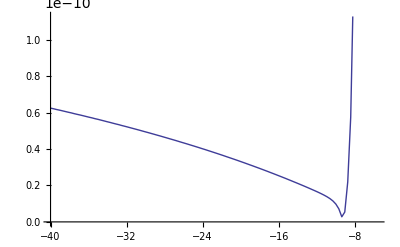

```mathematica
Monitor[ListLinePlot[Table[{data⟦k,1⟧,p[data⟦k,1⟧]-data⟦k,3⟧//Abs},{k,1,551,5}]],k]
```

## HM Tests

```mathematica
α=0;
σ=-1;
s[1]=Exp[-I π σ(α+1/2)];
s[2]=0;
s[3]=Exp[I π σ(α+1/2)];
{s[4],s[5],s[6]}=-Array[s,3];

S[k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[k_?OddQ]:=({{1, 0}, {s[k], 1}});

β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[y_,λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[y_,λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[y_,λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
ν=σ α/2;
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[y_,z_]:=Y[y,z].MatrixExp[(-g[y,z]) σ3];
Φp[y_,z_]:=Yp[y,z].MatrixExp[-(gp[y,z]) σ3];
Φm[y_,z_]:=Ym[y,z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG];
GGΣ[_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[y_,z_]=Φm[y,z].Inverse[S[1]].Inverse[Φm[y,z]]//Simplify;
GGΣin[y_,z_]=GGΣ[y,z]//Inverse;
GG[_][_,_?InfinityQ]:=IdentityMatrix[2];
GG[6][y_,z_]=Φ[y,z].S[6].Inverse[Φ[y,z]]//Simplify;
GG[1][y_,z_]=Φ[y,z].S[1].Inverse[Φ[y,z]]//Simplify;
GG[3][y_,z_]=Φ[y,z].S[3].Inverse[Φ[y,z]]//Simplify;
GG[4][y_,z_]=Φ[y,z].S[4].Inverse[Φ[y,z]]//Simplify;
```

```mathematica
GLC[1][y_,z_]=Inverse[Φm[y,z]];
GLC[2][y_,z_]=S[6].S[1].S[3].Inverse[Φ[y,z]];
GLC[3][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
```

```mathematica
GRC[1][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
GRC[2][y_,z_]=S[6].Inverse[Φ[y,z]];
GRC[3][y_,z_]=Inverse[Φm[y,z]];
```

```mathematica
rngg={.5,3.};

Cdefs[n_]:={({{-#, #}, {#, -#}})&,({{GGΣ, GGΣin}, {GG[3], GG[6]}, {GG[4], GG[1]}, {GLC[1], GRC[1]}, {GLC[2], GRC[2]}, {GLC[3], GRC[3]}}),({{Line[rngg], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})};
```

```mathematica
slv//Clear;slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];
```

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;
```

```mathematica
PainleveIIHM[n_,x_]:=2 ΦθSeries[x]-1/(π I) DomainIntegrate[slv[n][Sqrt[-x/2]]]⟦1,2⟧
```

```mathematica
pv=With[{n=50,x=-5.},-1/(π I) DomainIntegrate[slv[n][Sqrt[-x/2]]]⟦1,2⟧]
```

0.00165505+1.99282×10^-15 ⅈ

```mathematica
2 ΦθSeries[-5.]+ pv
```

-1.57948+1.99282×10^-15 ⅈ

```mathematica
?ConstructCurve
```

RiemannHilbert`ConstructCurve

ConstructCurve[{RiemannHilbert`Private`scs_,RiemannHilbert`Private`domain_},RiemannHilbert`Private`gfs_,RiemannHilbert`Private`x_]:=Join@@(ConstructCurve[#1,RiemannHilbert`Private`domain]&)/@Thread[{Transpose[RiemannHilbert`Private`scs[RiemannHilbert`Private`x]],Transpose[RiemannHilbert`Private`gfs]}]
 
ConstructCurve[{{RiemannHilbert`Private`z0_,RiemannHilbert`Private`sc_},RiemannHilbert`Private`gs_},RiemannHilbert`Private`domain_]:=(Fun[#1⟦1⟧,(#1⟦2,1⟧)/(RiemannHilbert`Private`sc)+RiemannHilbert`Private`z0,#1⟦2,2⟧]&)/@Thread[{RiemannHilbert`Private`gs,RiemannHilbert`Private`domain}]

```mathematica
G=ConstructCurve[Cdefs[40],Gl[Sqrt[-5./2]],Sqrt[-5./2]];
```

```mathematica
With[{n=40,x=-5.},DomainIntegrate[slv[n][Sqrt[-x/2]]]]
```

```mathematica
{{-0.07933883162221163-5.681219383824043*^-17 ⅈ,-4.0592529337857286*^-16-0.005199485199131456 ⅈ},{-1.272419669628988*^-15-0.005199485199126622 ⅈ,0.07933883162221098+9.62771529167128*^-16 ⅈ}}
```

```mathematica
G//RHSolve//DomainIntegrate
```

```mathematica
{{-0.07933883162221163-5.681219383824043*^-17 ⅈ,-4.0592529337857286*^-16-0.005199485199131456 ⅈ},{-1.272419669628988*^-15-0.005199485199126622 ⅈ,0.07933883162221098+9.62771529167128*^-16 ⅈ}} -{{-0.07933883162221261-2.108122704180815*^-15 ⅈ,1.4051260155412137*^-15-0.005199485199130344 ⅈ},{7.051650929845721*^-16-0.005199485199129649 ⅈ,0.07933883162221142+3.7643499428696714*^-16 ⅈ}}
```

{{9.85323×10^-16+2.05131×10^-15 ⅈ,-1.81105×10^-15-1.11196×10^-15 ⅈ},{-1.97758×10^-15+3.02709×10^-15 ⅈ,-4.44089×10^-16+5.86337×10^-16 ⅈ}}

```mathematica
G//DomainPlot
```

DomainPlot[ConstructCurve[{{{-#1,#1},{#1,-#1}}&,{{GGΣ,GGΣin},{GG[3],GG[6]},{GG[4],GG[1]},{GLC[1],GRC[1]},{GLC[2],GRC[2]},{GLC[3],GRC[3]}},{{Line[{0.5,3.}],40},{Line[{-0.25+0.433013 ⅈ,-1.5+2.59808 ⅈ}],40},{Line[{-0.25-0.433013 ⅈ,-1.5-2.59808 ⅈ}],40},{Line[{0.5,-0.25-0.433013 ⅈ}],40},{Line[{-0.25-0.433013 ⅈ,-0.25+0.433013 ⅈ}],40},{Line[{-0.25+0.433013 ⅈ,0.5}],40}}},{{GGΣ[0.+1.58114 ⅈ],GGΣin[0.+1.58114 ⅈ]},{GG[0.+1.58114 ⅈ,3],GG[0.+1.58114 ⅈ,6]},{GG[0.+1.58114 ⅈ,4],GG[0.+1.58114 ⅈ,1]},{GLC[0.+1.58114 ⅈ,1],GRC[0.+1.58114 ⅈ,1]},{GLC[0.+1.58114 ⅈ,2],GRC[0.+1.58114 ⅈ,2]},{GLC[0.+1.58114 ⅈ,3],GRC[0.+1.58114 ⅈ,3]}},0.+1.58114 ⅈ]]

```mathematica
G⟦1⟧//Last
```

{{0.999975,5.04551×10^-6-0.0000247179 ⅈ},{-5.04551×10^-6-0.0000247179 ⅈ,1.00003}}

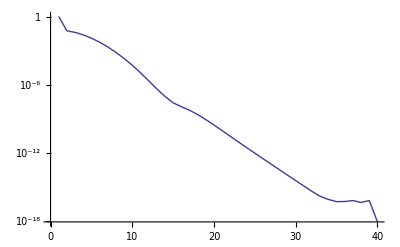
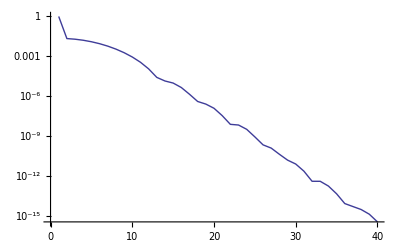
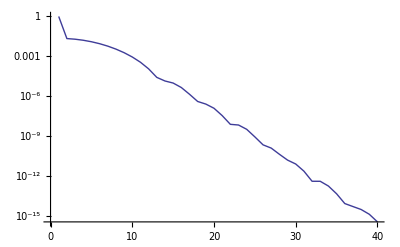
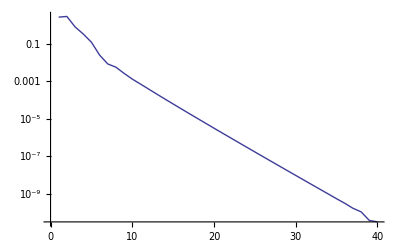
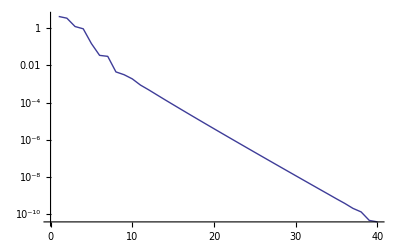
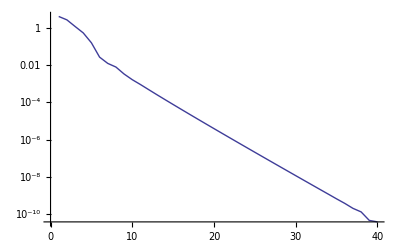
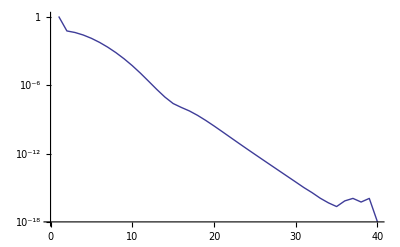
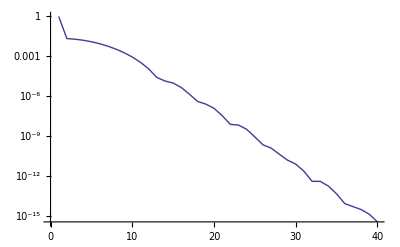
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@G
```

```mathematica
.
```

```mathematica
2 ΦθSeries[-5.]
```

```mathematica
-1.5811388300841898
```

```mathematica
PainleveIIHM[60,-7.]
```

```mathematica
-1.870137278580925+4.351175501724395*^-16 ⅈ
```

```mathematica
Select[data,First[#]==-20.&]⟦1,3⟧-PainleveIIHM[50,-20.]
```

1.01092×10^-10-2.39439×10^-15 ⅈ

```mathematica
Select[data,First[#]==-10.&]⟦1,3⟧-PainleveIIHM[50,-10.]
```

3.96081×10^-9+2.17697×10^-15 ⅈ

```mathematica
Select[data,First[#]==-7.&]⟦1,3⟧-PainleveIIHM[50,-7.]
```

8.56608×10^-8-1.75704×10^-15 ⅈ

```mathematica
{{-7.,9.080303779394358,-1.870137275910715,0.1338819675687076,2.206107647934002,0.6260118377500663,-2.010796706237386}}
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
-1.731025435933375-1.520702707074744*^-15 ⅈ
```

```mathematica
-1.731024958831779
```

```mathematica
-1.579490393158594+1.846488690071875*^-15 ⅈ
```

```mathematica
-1.579483782542241+1.992816292604485*^-15 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422612+6.90224540248159*^-16 ⅈ
```

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
Select[data,First[#]==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-5.,5.622378711823955,-1.579487087847008,0.1589913778691818,1.726754832688724,0.4571001663908862,-1.838905305470106}}
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[200,{-I,0.,I},-6.]
```

```mathematica
1.7310249641825814-6.51404263862787*^-10 ⅈ
```

```mathematica
1.5794870876539058+1.1152572199080169*^-9 ⅈ
```

```mathematica
1.5794856393446206-2.758557826609831*^-9 ⅈ
```

```mathematica
1.5794812822096675+2.9161579817582606*^-9 ⅈ
```

```mathematica
1.5794812863147345-5.184634943589117*^-10 ⅈ
```

```mathematica
1.5794812816197141-2.9485036634468997*^-10 ⅈ
```

```mathematica
1.5794812802206075+1.0231815394945443*^-12 ⅈ
```

```mathematica
1.5794812664580633+2.9692515113310947*^-10 ⅈ
```

```mathematica
PainleveII[{-I,0,I},-4.9999999]
```

```mathematica
1.5794870697048897+2.7642776956327*^-10 ⅈ
```

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.24306,-4.99999+6.83098×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.13712,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{1.73495,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,-50.]//Timing
```

{0.863311,-4.99999-5.77348×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,data⟦1,1⟧]-data⟦1,3⟧
```

6.24096×10^-11-2.84424×10^-15 ⅈ

```mathematica
PainleveIIHM[30,data⟦1,1⟧]-data⟦1,3⟧
```

-9.59233×10^-14+5.77175×10^-15 ⅈ

```mathematica
Monitor[ListLinePlot[Table[{data⟦k,1⟧,p[data⟦k,1⟧]-data⟦k,3⟧//Abs},{k,1,551,5}]],k]
```

-Graphics-

## s2

```mathematica
α=0;
σ=-1;
s[1]=Exp[-I π σ(α+1/2)];
s[2]=0;
s[3]=Exp[I π σ(α+1/2)];
{s[4],s[5],s[6]}=-Array[s,3];

S[k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[k_?OddQ]:=({{1, 0}, {s[k], 1}});

β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[y_,λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[y_,λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[y_,λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
ν=σ α/2;
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[y_,z_]:=Y[y,z].MatrixExp[(-g[y,z]) σ3];
Φp[y_,z_]:=Yp[y,z].MatrixExp[-(gp[y,z]) σ3];
Φm[y_,z_]:=Ym[y,z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG];
GGΣ[_][_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[y_][z_]=Φm[y,z].Inverse[S[1]].Inverse[Φm[y,z]]//Simplify;
GGΣin[y_][z_]=GGΣ[y][z]//Inverse;
GG[_,_][_?InfinityQ]:=IdentityMatrix[2];
GG[y_,6][z_]=Φ[y,z].S[6].Inverse[Φ[y,z]]//Simplify;
GG[y_,1][z_]=Φ[y,z].S[1].Inverse[Φ[y,z]]//Simplify;
GG[y_,3][z_]=Φ[y,z].S[3].Inverse[Φ[y,z]]//Simplify;
GG[y_,4][z_]=Φ[y,z].S[4].Inverse[Φ[y,z]]//Simplify;
```

```mathematica
GLC[y_,1][z_]=Inverse[Φm[y,z]];
GLC[y_,2][z_]=S[6].S[1].S[3].Inverse[Φ[y,z]];
GLC[y_,3][z_]=S[6].S[1].Inverse[Φp[y,z]];
```

```mathematica
GRC[y_,1][z_]=S[6].S[1].Inverse[Φp[y,z]];
GRC[y_,2][z_]=S[6].Inverse[Φ[y,z]];
GRC[y_,3][z_]=Inverse[Φm[y,z]];
```

```mathematica
S[1]//MatrixForm
```

(1 | 0
ⅈ | 1)

```mathematica
S[2].Inverse[S[4]]//MatrixForm
```

(1 | ⅈ
0 | 1)

```mathematica
σ2=({{0, -I}, {I, 0}});
```

```mathematica
σ2.Σ.σ2//MatrixForm
```

(0 | -ⅈ
-ⅈ | 0)

```mathematica
rngg={.5,3.};

Cdefs[n_]:={({{-#, #}, {#, -#}})&,({{Line[rngg], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})};
Gl[y_]:=({{GGΣ[y], GGΣin[y]}, {GG[y,3], GG[y,6]}, {GG[y,4], GG[y,1]}, {GLC[y,1], GRC[y,1]}, {GLC[y,2], GRC[y,2]}, {GLC[y,3], GRC[y,3]}});
```

```mathematica
slv//Clear;slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];
```

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;
```

```mathematica
PainleveIIHM[n_,x_]:=2 ΦθSeries[x]-1/(π I) Total[DomainIntegrate/@slv[n][Sqrt[-x/2],Gl[Sqrt[-x/2]]]]⟦1,2⟧
```

```mathematica
G=ConstructCurve[Cdefs[10],Gl[Sqrt[10./2]],Sqrt[10./2]];
```

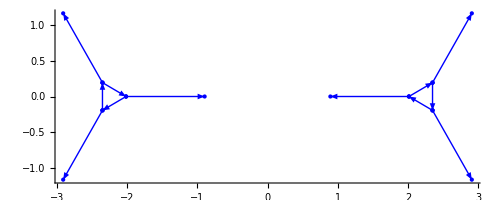

```mathematica
G//DomainPlot
```

```mathematica
PainleveIIHM[60,-6.]
```

```mathematica
-1.7310249588317772-7.512403896060963*^-16 ⅈ
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
Select[data,#⟦1⟧==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-7.,9.080303779394358,-1.870137275910715,0.1338819675687076,2.206107647934002,0.6260118377500663,-2.010796706237386}}
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
-1.731025435933375-1.520702707074744*^-15 ⅈ
```

```mathematica
-1.731024958831779
```

```mathematica
-1.579490393158594+1.846488690071875*^-15 ⅈ
```

```mathematica
-1.579483782542241+1.992816292604485*^-15 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422612+6.90224540248159*^-16 ⅈ
```

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
Select[data,First[#]==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-5.,5.622378711823955,-1.579487087847008,0.1589913778691818,1.726754832688724,0.4571001663908862,-1.838905305470106}}
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[200,{-I,0.,I},-6.]
```

```mathematica
1.7310249641825814-6.51404263862787*^-10 ⅈ
```

```mathematica
1.5794870876539058+1.1152572199080169*^-9 ⅈ
```

```mathematica
1.5794856393446206-2.758557826609831*^-9 ⅈ
```

```mathematica
1.5794812822096675+2.9161579817582606*^-9 ⅈ
```

```mathematica
1.5794812863147345-5.184634943589117*^-10 ⅈ
```

```mathematica
1.5794812816197141-2.9485036634468997*^-10 ⅈ
```

```mathematica
1.5794812802206075+1.0231815394945443*^-12 ⅈ
```

```mathematica
1.5794812664580633+2.9692515113310947*^-10 ⅈ
```

```mathematica
PainleveII[{-I,0,I},-4.9999999]
```

```mathematica
1.5794870697048897+2.7642776956327*^-10 ⅈ
```

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.24306,-4.99999+6.83098×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.13712,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{1.73495,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,-50.]//Timing
```

{0.863311,-4.99999-5.77348×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,data⟦1,1⟧]-data⟦1,3⟧
```

6.24096×10^-11-2.84424×10^-15 ⅈ

```mathematica
PainleveIIHM[30,data⟦1,1⟧]-data⟦1,3⟧
```

-9.59233×10^-14+5.77175×10^-15 ⅈ

```mathematica
Monitor[ListLinePlot[Table[{data⟦k,1⟧,p[data⟦k,1⟧]-data⟦k,3⟧//Abs},{k,1,551,5}]],k]
```

-Graphics-

## Rederivation

```mathematica
Subscript[s, 1] Subscript[s, 3]==1;
Subscript[s, 1]+Subscript[s, 3]==0;
```

```mathematica
Subscript[s^2, 1]==-1
```

```mathematica
Σ=({{0, 1/s[1]}, {-s[1], 0}})
```

{{0,1/s[1]},{-s[1],0}}

```mathematica
SubPlus[Φ]=SubMinus[Φ] G
```

```mathematica
SubPlus[P]=SubMinus[P] Σ
```

```mathematica
P  ({{ⅇ^g, 0}, {0, ⅇ^-g}})~P  ({{ⅇ^θ, 0}, {0, ⅇ^-θ}})~I
```

```mathematica
P = Y ({{ⅇ^-g, 0}, {0, ⅇ^g}})
```

```mathematica
Φ=Ψ P ({{ⅇ^θ, 0}, {0, ⅇ^-θ}})=Ψ Y ({{ⅇ^(θ-g), 0}, {0, ⅇ^(g-θ)}})
```

```mathematica
SubPlus[Φ]==SubMinus[Φ] G[1]
```

```mathematica
SubPlus[Ψ]==SubMinus[Ψ] P.S[1].Inverse[P]
```

```mathematica
G[1]==({{ⅇ^-θ, 0}, {0, ⅇ^θ}}).S[1].({{ⅇ^θ, 0}, {0, ⅇ^-θ}})
```

{{1,0},{ⅇ^(2 θ) s[1],1}}

```mathematica
SubPlus[Φ]==SubMinus[Φ] G[6].G[1]
```

```mathematica
SubPlus[Ψ]==SubMinus[Ψ] SubMinus[P].S[6].S[1].Inverse[SubPlus[P]]
```

```mathematica
SubPlus[Ψ]==SubMinus[Ψ] SubMinus[P].S[6].S[1].Σ.Inverse[SubMinus[P]]
```

```mathematica
S[6].S[1].Σ//MatrixForm
```

```mathematica
({{1, 0}, {-s[1], 1}}) ==Inverse[S[1]]
```

```mathematica
SubPlus[Φ]==SubMinus[Φ] G[1]
```

```mathematica
SubPlus[Ψ]==SubMinus[Ψ] P.S[2].Inverse[P]
```

```mathematica
y//Clear
```

```mathematica
(Φ[1.,0.000001 I].S[2].Inverse[Φ[1.,0.000001 I]]/.s[2]->4.)//Chop//MatrixForm
```

(1.-0.138967 ⅈ | 0.138967
0.138967 | 1.+0.138967 ⅈ)

```mathematica
(Φ[1.,-0.000001 I].S[5].Inverse[Φ[1.,-0.000001 I]]/.s[2]->4.)//Inverse//Chop//MatrixForm
```

(1.-0.138967 ⅈ | 0.138967
0.138967 | 1.+0.138967 ⅈ)

```mathematica
(Φp[1.,0.000001 I].S[2].Inverse[Φp[1.,0.000001 I]]/.s[2]->4.)//Chop//MatrixForm
```

(1.-0.138967 ⅈ | 0.138967
0.138967 | 1.+0.138967 ⅈ)

```mathematica
(Φp[1.,-0.000001 I].S[2].Inverse[Φp[1.,-0.000001 I]]/.s[2]->4.)//Chop//MatrixForm
```

(1.-0.138967 ⅈ | 0.138967
0.138967 | 1.+0.138967 ⅈ)

```mathematica
z//Clear
```

```mathematica
2 θ[x,z]
```

2 (ⅈ x z+(4 ⅈ z^3)/3)

## s2 again

```mathematica
α=0;
σ=-1;
s[1]=Exp[-I π σ(α+1/2)];
s[2]=2.;
s[3]=Exp[I π σ(α+1/2)];
{s[4],s[5],s[6]}=-Array[s,3];

S[k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[k_?OddQ]:=({{1, 0}, {s[k], 1}});

β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[y_,λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[y_,λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[y_,λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
ν=σ α/2;
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[y_,z_]:=Y[y,z].MatrixExp[(-g[y,z]) σ3];
Φp[y_,z_]:=Yp[y,z].MatrixExp[-(gp[y,z]) σ3];
Φm[y_,z_]:=Ym[y,z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG];
GGΣ[_][_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[y_][z_]=Φm[y,z].Inverse[S[1]].Inverse[Φm[y,z]]//Simplify;
GGΣin[y_][z_]=GGΣ[y][z]//Inverse;
GG[_,_][_?InfinityQ]:=IdentityMatrix[2];
GG[y_,6][z_]=Φ[y,z].S[6].Inverse[Φ[y,z]]//Simplify;
GG[y_,1][z_]=Φ[y,z].S[1].Inverse[Φ[y,z]]//Simplify;
GG[y_,3][z_]=Φ[y,z].S[3].Inverse[Φ[y,z]]//Simplify;
GG[y_,4][z_]=Φ[y,z].S[4].Inverse[Φ[y,z]]//Simplify;
```

```mathematica
GLC[y_,1][z_]=Inverse[Φm[y,z]];
GLC[y_,2][z_]=S[6].S[1].S[3].Inverse[Φ[y,z]];
GLC[y_,3][z_]=S[6].S[1].Inverse[Φp[y,z]];
```

```mathematica
GRC[y_,1][z_]=S[6].S[1].Inverse[Φp[y,z]];
GRC[y_,2][z_]=S[6].Inverse[Φ[y,z]];
GRC[y_,3][z_]=Inverse[Φm[y,z]];
```

```mathematica
Ψpin[y_,z_]=Inverse[Φp[y,z]];
GMid[y_][z_]=Φp[y,z].S[2].Ψpin[y,z];
```

```mathematica
y//Clear
```

```mathematica
Series[gp[y,z],{z,0,4}]
```

(4 y^3)/3-2 y z^2+z^4/(2 y)+O[z]^5

```mathematica
y//Clear
```

```mathematica
Clear[y]
```

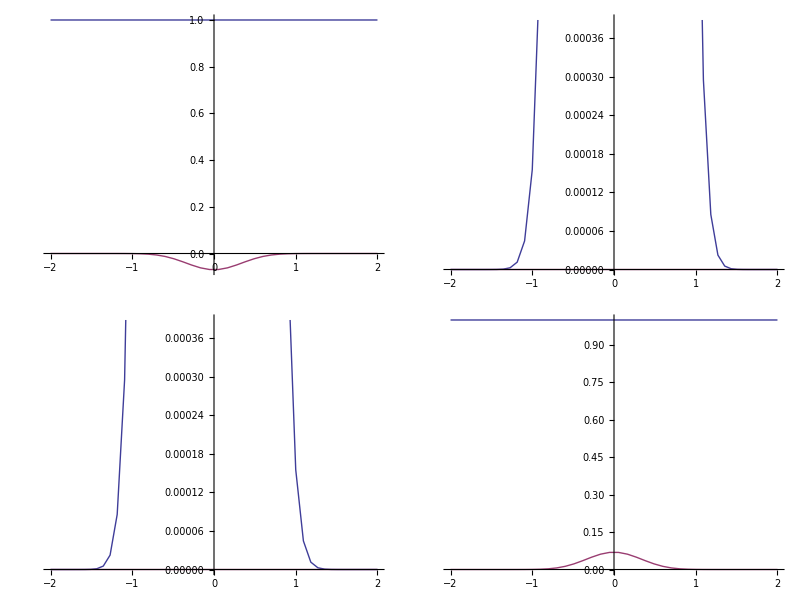
(-Graphics-)

```mathematica
y=1.;IFun[Φp[y,#].S[2].Ψpin[y,#]&,Line[2.{-I,I}/Sqrt[y]]]
```

```mathematica
rngg={.5,3.};

Cdefs[n_]:={{Function[y,({{-y, y}, {y, -y}})],({{Line[rngg], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})},
{Function[y,({{0}, {Sqrt[y]}})],({{Line[2 {-I,I}], n}})}};
Gl[y_]:={({{GGΣ[y], GGΣin[y]}, {GG[y,3], GG[y,6]}, {GG[y,4], GG[y,1]}, {GLC[y,1], GRC[y,1]}, {GLC[y,2], GRC[y,2]}, {GLC[y,3], GRC[y,3]}}),{{GMid[y]}}};
```

```mathematica
?Cdefs
```

```mathematica
?Gl
```

```mathematica
x=-1.;
```

```mathematica
x=-10.;
```

```mathematica
ConstructCurve[Cdefs[10]⟦1⟧,Gl[Sqrt[-x/2]]⟦1⟧,Sqrt[-x/2]]
```

```mathematica
Gl[Sqrt[-x/2]]⟦2⟧
```

{{GMid[2.23607]}}

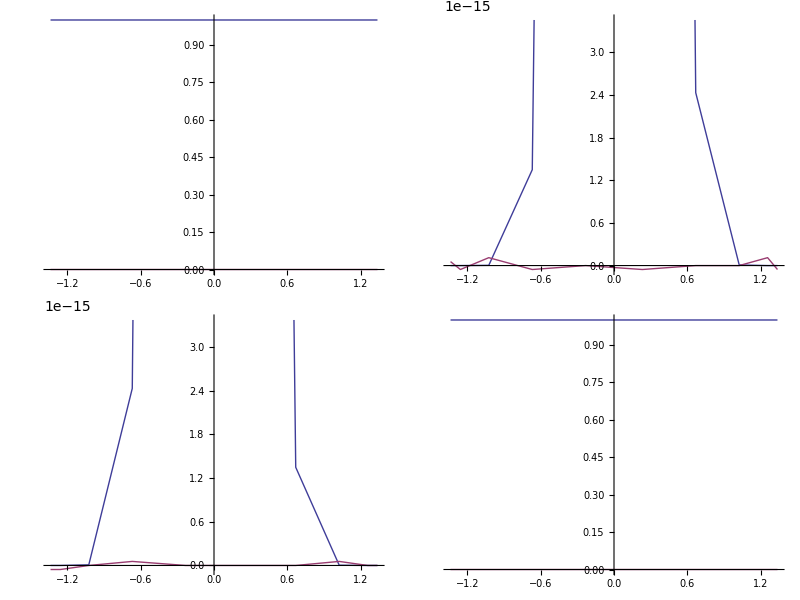
{(-Graphics-)}

```mathematica
ConstructCurve[Cdefs[10]⟦2⟧,Gl[Sqrt[-x/2]]⟦2⟧,Sqrt[-x/2]]
```

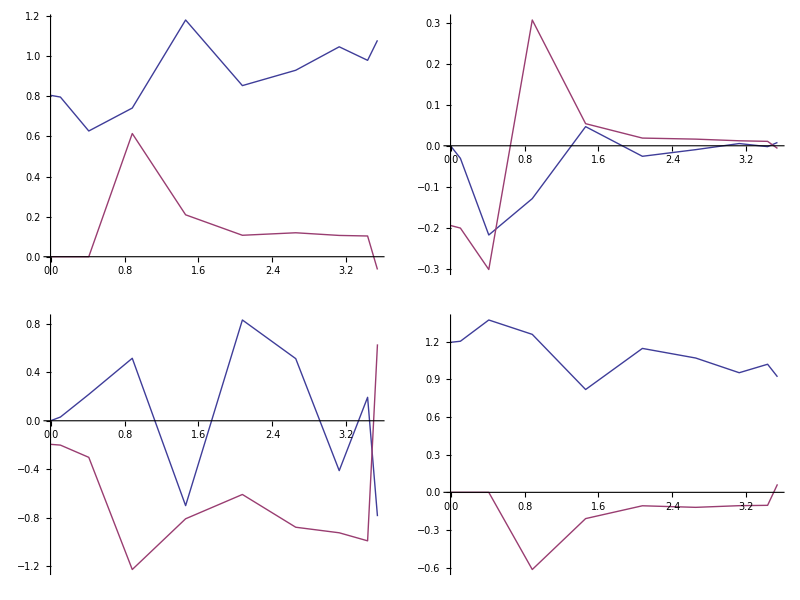
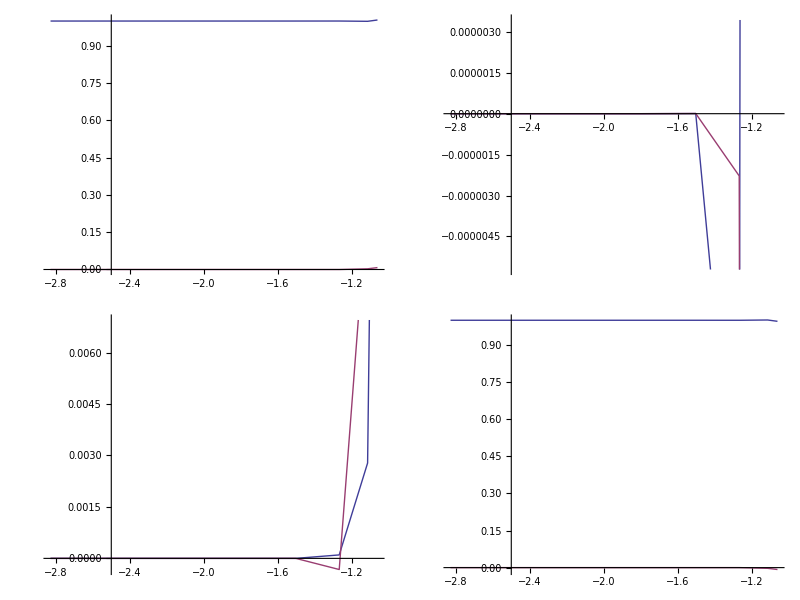
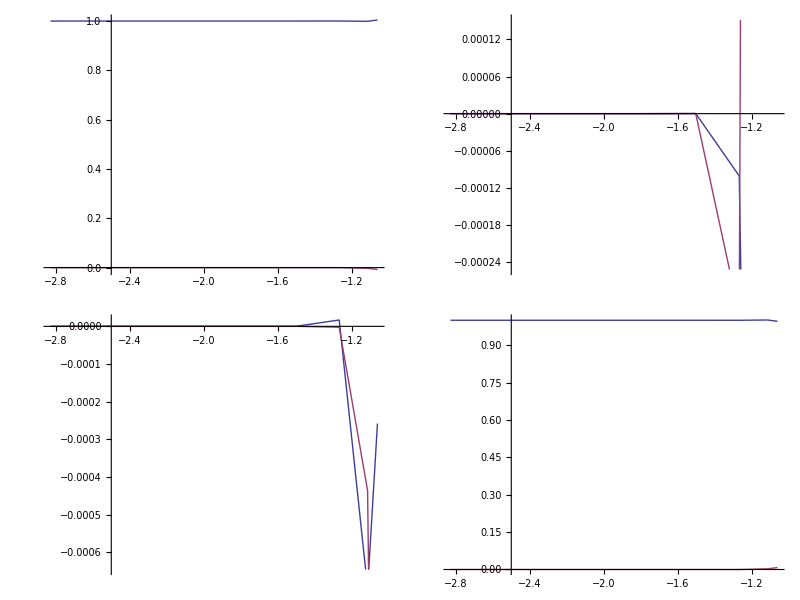
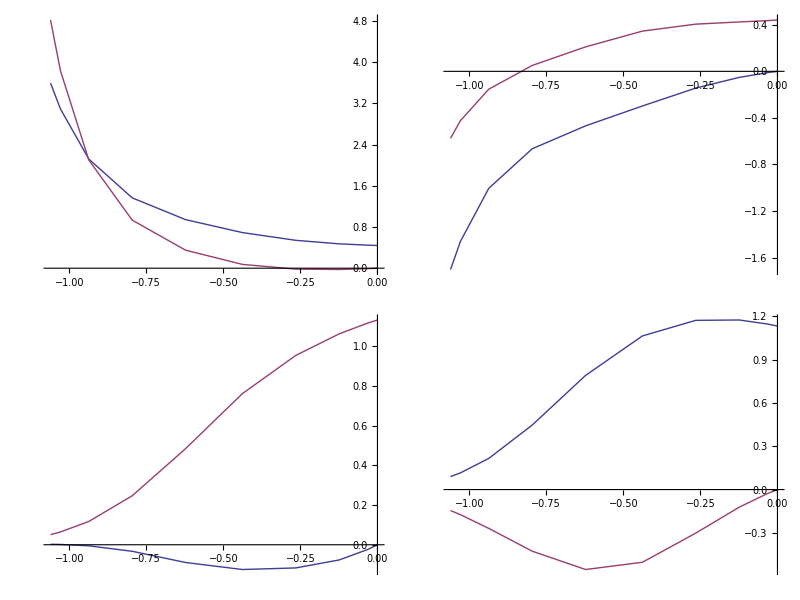
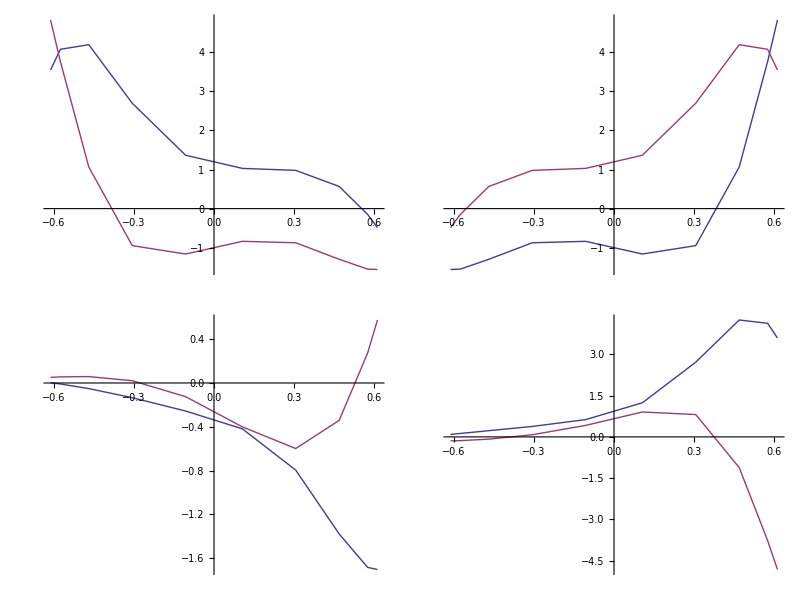
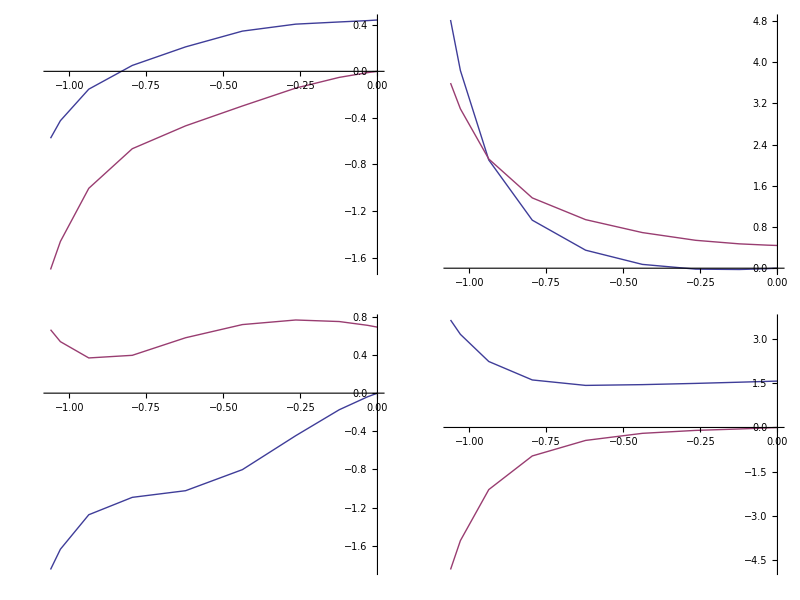
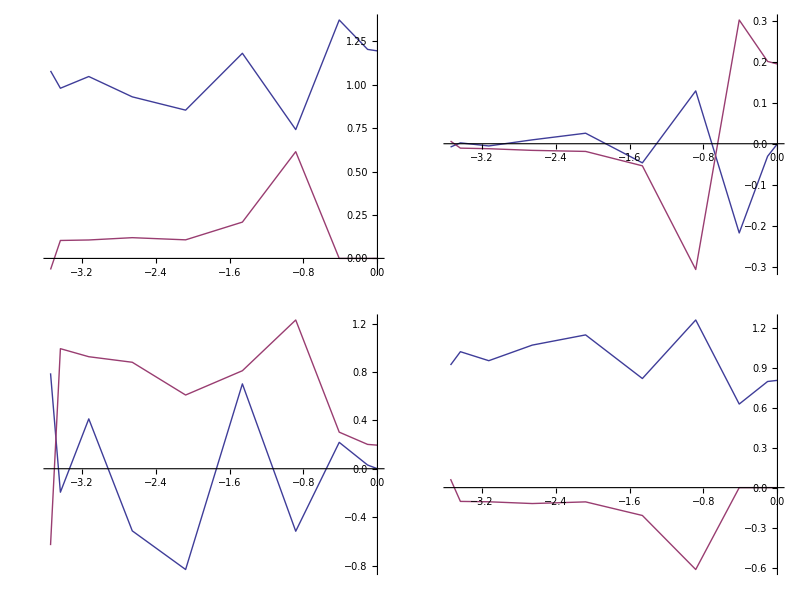
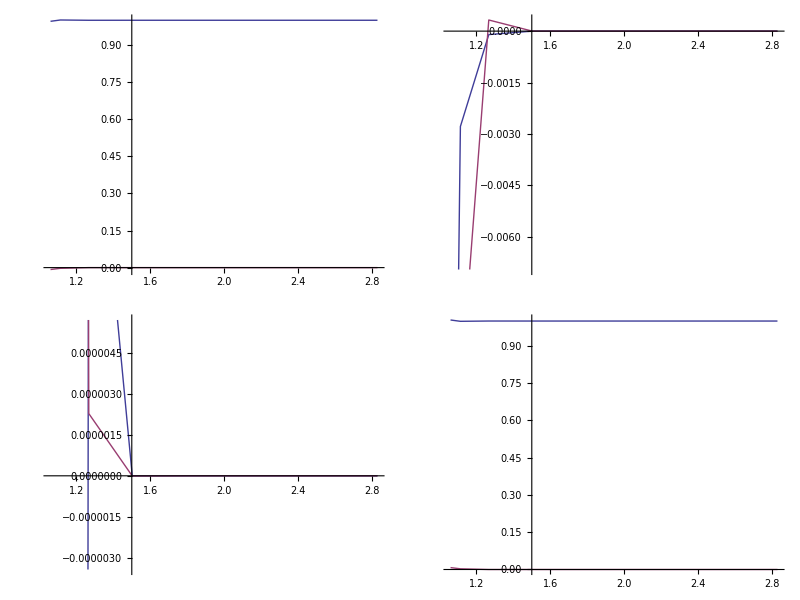
{{(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-)},{-Graphics-}}

```mathematica
ConstructCurve[Sequence@@#,Sqrt[-x/2]]&/@Thread[{Cdefs[10],Gl[Sqrt[-x/2]]}]
```

```mathematica
ConstructCurve[crvs:{{_,_}..},gls_List,x_]:=Join@@(ConstructCurve[#,x]&/@crvs);
```

```mathematica
x=-1.;ConstructCurve[Cdefs[10],Gl[Sqrt[-x/2]],Sqrt[-x/2]]
```

Part::partd: Part specification {Function[y, {{0}, {√y}}], 0.707107} ⟦ 2, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification {Function[y, {{0}, {√y}}], 0.707107} ⟦ 2, 2 ⟧ is longer than depth of object.

Range::range: Range specification in Range[-1, -1 + {Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧/{Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧, 2/{Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧] does not have appropriate bounds.

Part::partd: Part specification {Function[y, {{0.}, {√y}}], 0.707107} ⟦ 2, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Range::range: Range specification in Range[-1., -1. + {Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧/{Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧, 2./{Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧] does not have appropriate bounds.

General::stop: Further output of Range :: range will be suppressed during this calculation.

Part::partw: Part {1, 2, -1, -2} of ToList[FFT[{MapFromInterval[{{Line[{« 2 »}], 10}}[{{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}, GMid[0.707107]}, Line[{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}]], {{Line[{« 2 »}], 10}}[{{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}, GMid[0.707107]}, -ⅈ\ Log[Power[« 2 »]]/π]][MapFromInterval[Line[{{« 2 »}, « 4 », {« 2 »}}], « 1 »]], « 6 », « 1 »}]] does not exist.

Part::partw: Part {1, 2, -1, -2} of ToList[FFT[{MapFromInterval[{{Line[{« 2 »}], 10}}[{{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}, GMid[0.707107]}, Line[{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}]], {{Line[{« 2 »}], 10}}[{{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}, GMid[0.707107]}, -ⅈ\ Log[Power[« 2 »]]/π]][MapFromInterval[Line[{{« 2 »}, « 4 », {« 2 »}}], 1.]], « 6 », « 1 »}]] does not exist.

Part::partd: Part specification {Function[y, {{0.}, {√y}}], 0.707107} ⟦ 2, 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

{-Graphics-,-Graphics-}

```mathematica
slv//Clear;slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];
```

```mathematica
x//Clear
```

```mathematica
With[{x=-7.,n=35},2 ΦθSeries[x]-1/(π I)Total[DomainIntegrate/@slv[n][Sqrt[-x/2],Gl[Sqrt[-x/2]]]]⟦1,2⟧]
```

```mathematica
-1.8701372838946757+9.690752545084153*^-17 ⅈ
```

```mathematica
-1.8701372838947063+2.6073922232414456*^-15 ⅈ
```

```mathematica
-1.870137283898853-1.6203711306865781*^-15 ⅈ
```

```mathematica
-1.8701372838895252+5.444574000422308*^-14 ⅈ
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[210,{I,2.,-I},-5.]
```

```mathematica
-1.579492894693782+6.205436164918865*^-10 ⅈ
```

```mathematica
-1.5794928930453276+8.909193383033198*^-10 ⅈ
```

```mathematica
-1.579492890621747+4.205634951404136*^-9 ⅈ
```

```mathematica
-1.5794928935016475-3.107162527271612*^-9 ⅈ
```

```mathematica
-1.5794928919531561-4.108420270654278*^-9 ⅈ
```

```mathematica
-1.8701373251254703-1.1183090009581065*^-9 ⅈ
```

```mathematica
-1.8701372925685944+2.2557401280209888*^-8 ⅈ
```

```mathematica
-1.8701372761264747-2.57034855621896*^-8 ⅈ
```

```mathematica
-1.8701373110752249-9.521869515083381*^-9 ⅈ
```

```mathematica
-2.1208774621190436-8.707231245352887*^-6 ⅈ
```

```mathematica
x=-6.5;
```

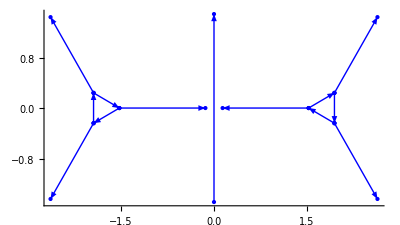

```mathematica
DomainPlot[slv[20][Sqrt[-x/2],Gl[Sqrt[-x/2]]]]
```

```mathematica
-1.999507198112405+3.369179243822534*^-14 ⅈ
```

```mathematica
-1.9995069860079446-4.6643222862033724*^-11 ⅈ
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[150,{I,0.,-I},-8.]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 23 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 844 »}, « 50 »}
 may contain significant numerical errors.

```mathematica
-1.9995064012853057-8.690153663337696*^-8 ⅈ
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[150,{I,2.,-I},-8.]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 23 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 844 »}, « 50 »}
 may contain significant numerical errors.

```mathematica
-1.9995062405749535-7.20408479537582*^-8 ⅈ
```

```mathematica
s[1]
```

ⅈ

```mathematica
s[2]
```

2.

```mathematica
s[3]
```

-ⅈ

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;
```

```mathematica
PainleveIIHM[n_,x_]:=2 ΦθSeries[x]-1/(π I) Total[DomainIntegrate/@slv[n][Sqrt[-x/2],Gl[Sqrt[-x/2]]]]⟦1,2⟧
```

```mathematica
G=ConstructCurve[Cdefs[10],Gl[Sqrt[10./2]],Sqrt[10./2]];
```

```mathematica
G//DomainPlot
```

-Graphics-

```mathematica
PainleveIIHM[60,-6.]
```

```mathematica
-1.7310249588317772-7.512403896060963*^-16 ⅈ
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
Select[data,#⟦1⟧==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-7.,9.080303779394358,-1.870137275910715,0.1338819675687076,2.206107647934002,0.6260118377500663,-2.010796706237386}}
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
-1.731025435933375-1.520702707074744*^-15 ⅈ
```

```mathematica
-1.731024958831779
```

```mathematica
-1.579490393158594+1.846488690071875*^-15 ⅈ
```

```mathematica
-1.579483782542241+1.992816292604485*^-15 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422612+6.90224540248159*^-16 ⅈ
```

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
Select[data,First[#]==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-5.,5.622378711823955,-1.579487087847008,0.1589913778691818,1.726754832688724,0.4571001663908862,-1.838905305470106}}
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[200,{-I,0.,I},-6.]
```

```mathematica
1.7310249641825814-6.51404263862787*^-10 ⅈ
```

```mathematica
1.5794870876539058+1.1152572199080169*^-9 ⅈ
```

```mathematica
1.5794856393446206-2.758557826609831*^-9 ⅈ
```

```mathematica
1.5794812822096675+2.9161579817582606*^-9 ⅈ
```

```mathematica
1.5794812863147345-5.184634943589117*^-10 ⅈ
```

```mathematica
1.5794812816197141-2.9485036634468997*^-10 ⅈ
```

```mathematica
1.5794812802206075+1.0231815394945443*^-12 ⅈ
```

```mathematica
1.5794812664580633+2.9692515113310947*^-10 ⅈ
```

```mathematica
PainleveII[{-I,0,I},-4.9999999]
```

```mathematica
1.5794870697048897+2.7642776956327*^-10 ⅈ
```

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.24306,-4.99999+6.83098×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.13712,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{1.73495,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,-50.]//Timing
```

{0.863311,-4.99999-5.77348×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,data⟦1,1⟧]-data⟦1,3⟧
```

6.24096×10^-11-2.84424×10^-15 ⅈ

```mathematica
PainleveIIHM[30,data⟦1,1⟧]-data⟦1,3⟧
```

-9.59233×10^-14+5.77175×10^-15 ⅈ

```mathematica
Monitor[ListLinePlot[Table[{data⟦k,1⟧,p[data⟦k,1⟧]-data⟦k,3⟧//Abs},{k,1,551,5}]],k]
```

-Graphics-

## s2 again test small x

```mathematica
α=0;
σ=-1;
s[1]=Exp[-I π σ(α+1/2)];
s[2]=2.;
s[3]=Exp[I π σ(α+1/2)];
{s[4],s[5],s[6]}=-Array[s,3];

S[k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[k_?OddQ]:=({{1, 0}, {s[k], 1}});

β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[y_,λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[y_,λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[y_,λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
ν=σ α/2;
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[y_,z_]:=Y[y,z].MatrixExp[(-g[y,z]) σ3];
Φp[y_,z_]:=Yp[y,z].MatrixExp[-(gp[y,z]) σ3];
Φm[y_,z_]:=Ym[y,z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG];
GGΣ[_][_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[y_][z_]=Φm[y,z].Inverse[S[1]].Inverse[Φm[y,z]]//Simplify;
GGΣin[y_][z_]=GGΣ[y][z]//Inverse;
GG[_,_][_?InfinityQ]:=IdentityMatrix[2];
GG[y_,6][z_]=Φ[y,z].S[6].Inverse[Φ[y,z]]//Simplify;
GG[y_,1][z_]=Φ[y,z].S[1].Inverse[Φ[y,z]]//Simplify;
GG[y_,3][z_]=Φ[y,z].S[3].Inverse[Φ[y,z]]//Simplify;
GG[y_,4][z_]=Φ[y,z].S[4].Inverse[Φ[y,z]]//Simplify;
```

```mathematica
GLC[y_,1][z_]=Inverse[Φm[y,z]];
GLC[y_,2][z_]=S[6].S[1].S[3].Inverse[Φ[y,z]];
GLC[y_,3][z_]=S[6].S[1].Inverse[Φp[y,z]];
```

```mathematica
GRC[y_,1][z_]=S[6].S[1].Inverse[Φp[y,z]];
GRC[y_,2][z_]=S[6].Inverse[Φ[y,z]];
GRC[y_,3][z_]=Inverse[Φm[y,z]];
```

```mathematica
Ψpin[y_,z_]=Inverse[Φp[y,z]];
GMid[y_][z_]=Φp[y,z].S[2].Ψpin[y,z];
```

```mathematica
rngg={.5,3.};

Cdefs[n_]:={{Function[y,({{-y, y}, {y, -y}})],({{Line[{.5,1.}], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})},
{Function[y,({{0}, {Sqrt[y]}})],({{Line[2 {-I,I}], n}})}};
Gl[y_]:={({{GGΣ[y], GGΣin[y]}, {GG[y,3], GG[y,6]}, {GG[y,4], GG[y,1]}, {GLC[y,1], GRC[y,1]}, {GLC[y,2], GRC[y,2]}, {GLC[y,3], GRC[y,3]}}),{{GMid[y]}}};
```

```mathematica
?Cdefs
```

```mathematica
?Gl
```

```mathematica
x=-2.;
```

```mathematica
x=-10.;
```

```mathematica
ConstructCurve[Cdefs[10]⟦1⟧,Gl[Sqrt[-x/2]]⟦1⟧,Sqrt[-x/2]]//First//Values//Last
```

{{0.963662,0.00363381-0.0361559 ⅈ},{-0.00363381-0.0361559 ⅈ,1.03634}}

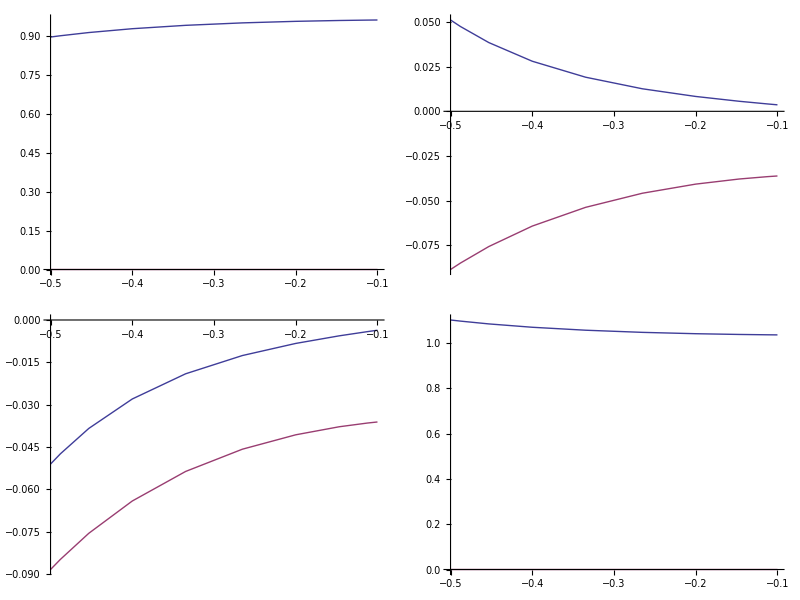
(-Graphics-)

```mathematica
/
```

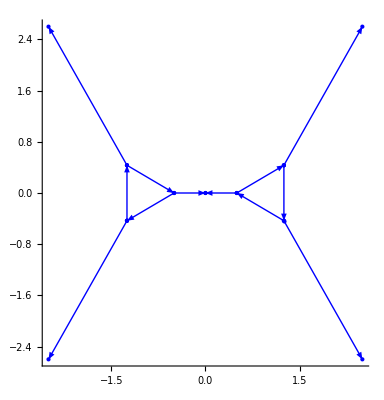

```mathematica
ConstructCurve[Cdefs[10]⟦1⟧,Gl[Sqrt[-x/2]]⟦1⟧,Sqrt[-x/2]] //DomainPlot
```

```mathematica
Gl[Sqrt[-x/2]]⟦2⟧
```

{{GMid[2.23607]}}

```mathematica
ConstructCurve[Cdefs[10]⟦2⟧,Gl[Sqrt[-x/2]]⟦2⟧,Sqrt[-x/2]]
```

{(-Graphics-)}

```mathematica
ConstructCurve[Sequence@@#,Sqrt[-x/2]]&/@Thread[{Cdefs[10],Gl[Sqrt[-x/2]]}]
```

{{(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-),(-Graphics-)},{-Graphics-}}

```mathematica
ConstructCurve[crvs:{{_,_}..},gls_List,x_]:=Join@@(ConstructCurve[#,x]&/@crvs);
```

```mathematica
x=-1.;ConstructCurve[Cdefs[10],Gl[Sqrt[-x/2]],Sqrt[-x/2]]
```

Part::partd: Part specification {Function[y, {{0}, {√y}}], 0.707107} ⟦ 2, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification {Function[y, {{0}, {√y}}], 0.707107} ⟦ 2, 2 ⟧ is longer than depth of object.

Range::range: Range specification in Range[-1, -1 + {Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧/{Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧, 2/{Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧] does not have appropriate bounds.

Part::partd: Part specification {Function[y, {{0.}, {√y}}], 0.707107} ⟦ 2, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Range::range: Range specification in Range[-1., -1. + {Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧/{Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧, 2./{Function[y, {{« 1 »}, {« 1 »}}], 0.707107} ⟦ 2, 2 ⟧] does not have appropriate bounds.

General::stop: Further output of Range :: range will be suppressed during this calculation.

Part::partw: Part {1, 2, -1, -2} of ToList[FFT[{MapFromInterval[{{Line[{« 2 »}], 10}}[{{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}, GMid[0.707107]}, Line[{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}]], {{Line[{« 2 »}], 10}}[{{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}, GMid[0.707107]}, -ⅈ\ Log[Power[« 2 »]]/π]][MapFromInterval[Line[{{« 2 »}, « 4 », {« 2 »}}], « 1 »]], « 6 », « 1 »}]] does not exist.

Part::partw: Part {1, 2, -1, -2} of ToList[FFT[{MapFromInterval[{{Line[{« 2 »}], 10}}[{{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}, GMid[0.707107]}, Line[{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}]], {{Line[{« 2 »}], 10}}[{{{« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}, {« 2 »}}, GMid[0.707107]}, -ⅈ\ Log[Power[« 2 »]]/π]][MapFromInterval[Line[{{« 2 »}, « 4 », {« 2 »}}], 1.]], « 6 », « 1 »}]] does not exist.

Part::partd: Part specification {Function[y, {{0.}, {√y}}], 0.707107} ⟦ 2, 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

{-Graphics-,-Graphics-}

```mathematica
slv//Clear;slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];
```

```mathematica
x//Clear
```

```mathematica
With[{x=-7.,n=35},2 ΦθSeries[x]-1/(π I)Total[DomainIntegrate/@slv[n][Sqrt[-x/2],Gl[Sqrt[-x/2]]]]⟦1,2⟧]
```

```mathematica
-1.8701372838946757+9.690752545084153*^-17 ⅈ
```

```mathematica
-1.8701372838947063+2.6073922232414456*^-15 ⅈ
```

```mathematica
-1.870137283898853-1.6203711306865781*^-15 ⅈ
```

```mathematica
-1.8701372838895252+5.444574000422308*^-14 ⅈ
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[210,{I,2.,-I},-5.]
```

```mathematica
-1.579492894693782+6.205436164918865*^-10 ⅈ
```

```mathematica
-1.5794928930453276+8.909193383033198*^-10 ⅈ
```

```mathematica
-1.579492890621747+4.205634951404136*^-9 ⅈ
```

```mathematica
-1.5794928935016475-3.107162527271612*^-9 ⅈ
```

```mathematica
-1.5794928919531561-4.108420270654278*^-9 ⅈ
```

```mathematica
-1.8701373251254703-1.1183090009581065*^-9 ⅈ
```

```mathematica
-1.8701372925685944+2.2557401280209888*^-8 ⅈ
```

```mathematica
-1.8701372761264747-2.57034855621896*^-8 ⅈ
```

```mathematica
-1.8701373110752249-9.521869515083381*^-9 ⅈ
```

```mathematica
-2.1208774621190436-8.707231245352887*^-6 ⅈ
```

```mathematica
x=-6.5;
```

```mathematica
DomainPlot[slv[20][Sqrt[-x/2],Gl[Sqrt[-x/2]]]]
```

-Graphics-

```mathematica
-1.999507198112405+3.369179243822534*^-14 ⅈ
```

```mathematica
-1.9995069860079446-4.6643222862033724*^-11 ⅈ
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[150,{I,0.,-I},-8.]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 23 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 844 »}, « 50 »}
 may contain significant numerical errors.

```mathematica
-1.9995064012853057-8.690153663337696*^-8 ⅈ
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[150,{I,2.,-I},-8.]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 23 », 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, « 844 »}, « 50 »}
 may contain significant numerical errors.

```mathematica
-1.9995062405749535-7.20408479537582*^-8 ⅈ
```

```mathematica
s[1]
```

ⅈ

```mathematica
s[2]
```

2.

```mathematica
s[3]
```

-ⅈ

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;
```

```mathematica
PainleveIIHM[n_,x_]:=2 ΦθSeries[x]-1/(π I) Total[DomainIntegrate/@slv[n][Sqrt[-x/2],Gl[Sqrt[-x/2]]]]⟦1,2⟧
```

```mathematica
G=ConstructCurve[Cdefs[10],Gl[Sqrt[10./2]],Sqrt[10./2]];
```

```mathematica
G//DomainPlot
```

-Graphics-

```mathematica
PainleveIIHM[60,-6.]
```

```mathematica
-1.7310249588317772-7.512403896060963*^-16 ⅈ
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
Select[data,#⟦1⟧==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-7.,9.080303779394358,-1.870137275910715,0.1338819675687076,2.206107647934002,0.6260118377500663,-2.010796706237386}}
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
-1.731025435933375-1.520702707074744*^-15 ⅈ
```

```mathematica
-1.731024958831779
```

```mathematica
-1.579490393158594+1.846488690071875*^-15 ⅈ
```

```mathematica
-1.579483782542241+1.992816292604485*^-15 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422612+6.90224540248159*^-16 ⅈ
```

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
Select[data,First[#]==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-5.,5.622378711823955,-1.579487087847008,0.1589913778691818,1.726754832688724,0.4571001663908862,-1.838905305470106}}
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[200,{-I,0.,I},-6.]
```

```mathematica
1.7310249641825814-6.51404263862787*^-10 ⅈ
```

```mathematica
1.5794870876539058+1.1152572199080169*^-9 ⅈ
```

```mathematica
1.5794856393446206-2.758557826609831*^-9 ⅈ
```

```mathematica
1.5794812822096675+2.9161579817582606*^-9 ⅈ
```

```mathematica
1.5794812863147345-5.184634943589117*^-10 ⅈ
```

```mathematica
1.5794812816197141-2.9485036634468997*^-10 ⅈ
```

```mathematica
1.5794812802206075+1.0231815394945443*^-12 ⅈ
```

```mathematica
1.5794812664580633+2.9692515113310947*^-10 ⅈ
```

```mathematica
PainleveII[{-I,0,I},-4.9999999]
```

```mathematica
1.5794870697048897+2.7642776956327*^-10 ⅈ
```

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.24306,-4.99999+6.83098×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.13712,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{1.73495,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,-50.]//Timing
```

{0.863311,-4.99999-5.77348×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,data⟦1,1⟧]-data⟦1,3⟧
```

6.24096×10^-11-2.84424×10^-15 ⅈ

```mathematica
PainleveIIHM[30,data⟦1,1⟧]-data⟦1,3⟧
```

-9.59233×10^-14+5.77175×10^-15 ⅈ

```mathematica
Monitor[ListLinePlot[Table[{data⟦k,1⟧,p[data⟦k,1⟧]-data⟦k,3⟧//Abs},{k,1,551,5}]],k]
```

-Graphics-

## Test x decay

```mathematica
rngg
```

{0.5,3.}

```mathematica
Cdefs[n_]:={{Function[y,({{-y, y}, {y, -y}})],({{Line[{.5,4.}], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})},
{Function[y,({{0}, {Sqrt[y]}})],({{Line[2 {-I,I}], n}})}};
Gl[y_]:={({{GGΣ[y], GGΣin[y]}, {GG[y,3], GG[y,6]}, {GG[y,4], GG[y,1]}, {GLC[y,1], GRC[y,1]}, {GLC[y,2], GRC[y,2]}, {GLC[y,3], GRC[y,3]}}),{{GMid[y]}}};
```

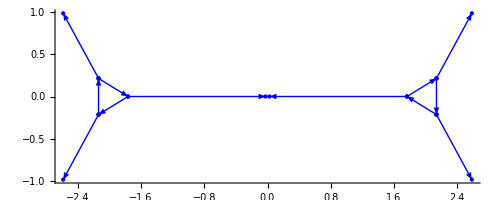

```mathematica
x=-8.1;ConstructCurve[Cdefs[10]⟦1⟧,Gl[Sqrt[-x/2]]⟦1⟧,Sqrt[-x/2]]//DomainPlot
```

```mathematica
x=-8.1;ConstructCurve[Cdefs[10]⟦1⟧,Gl[Sqrt[-x/2]]⟦1⟧,Sqrt[-x/2]]⟦1⟧//Last
```

{{1.,2.25667×10^-12-1.82776×10^-10 ⅈ},{-2.25667×10^-12-1.82776×10^-10 ⅈ,1.}}

## Small x

```mathematica
{{Line[{.5,4.}], n}}
```

```mathematica
{{GGΣ[y], GGΣin[y]}}
```

```mathematica
rngg
```

{0.5,2.3}

```mathematica
Cdefs[n_]:={{Function[y,({{-y, y}, {y, -y}})],({{Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})},
{Function[y,({{0}, {Sqrt[y]}})],({{Line[2 {-I,0}], n}, {Line[2 {0,I}], n}})}};
Gl[y_]:={({{GG[y,3], GG[y,6]}, {GG[y,4], GG[y,1]}, {GLC[y,1], GRC[y,1]}, {GLC[y,2], GRC[y,2]}, {GLC[y,3], GRC[y,3]}}),({{GMid[y]}, {GMid[y]}})};
```

```mathematica
x=-1.1;
```

```mathematica
y=Sqrt[-x/2];
n=20;
Timing[
2 ΦθSeries[x]-1/(π I)(Join[ConstructCurve[Cdefs[n],Gl[y],y],
Fun[GGΣ[y],Line[{-y+rngg⟦1⟧/y,0,y-rngg⟦1⟧/y}],n]]//RHSolveTop//DomainIntegrate)⟦2⟧
]
```

```mathematica
{3.5240459999999985,-0.8195182094446984-5.742668174864683*^-16 ⅈ}
```

{1.49921,-0.819543+6.53781×10^-16 ⅈ}

```mathematica
s[1]
```

ⅈ

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[150,{s[1],s[2],s[3]},x]
```

```mathematica
-0.7201820779576396+1.3877787807814457*^-17 ⅈ
```

```mathematica
-0.8195182144198023-6.912040384499107*^-12 ⅈ
```

```mathematica
%
```

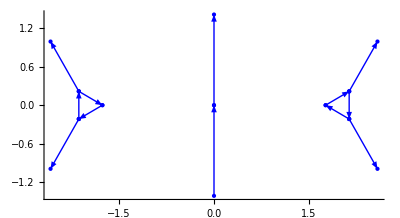

```mathematica
DomainPlot[ConstructCurve[Cdefs[10],Gl[Sqrt[-x/2]],Sqrt[-x/2]]]
```

```mathematica
?ConstructCurve
```

RiemannHilbert`ConstructCurve

ConstructCurve[crvs:{{_,_}..},gls_List,x_]:=Join@@(ConstructCurve[#1,x]&)/@crvs
 
ConstructCurve[{scs_,domain_},gfs_,x_]:=Join@@(ConstructCurve[#1,domain]&)/@Thread[{Transpose[scs[x]],Transpose[gfs]}]
 
ConstructCurve[{{z0_,sc_},gs_},domain_]:=(Fun[#1⟦1⟧,(#1⟦2,1⟧)/sc+z0,#1⟦2,2⟧]&)/@Thread[{gs,domain}]

```mathematica
Cdef
```